```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[21],Join[Table[{i,i-1},{i,Range[2,21,1]}],Table[{i,i+1},{i,Range[1,21,1]}]]->-t]
```

```mathematica
β[ω,0.001,1,0]
```

{{(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω}}

```mathematica
T[t_]:=T[t]=t*IdentityMatrix[21]
```

```mathematica
T1[t_]:=T[t]
```

```mathematica
T2[t_]:=T[t]
```

```mathematica
T[1]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],A:=Inverse[β[ω,0.001,1,0]],T:=T[1]},Do[J=Inverse[IdentityMatrix[21]-A.T.J.T].A,13200];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[21]-g[ω,δ,t,ϵ].T[t].LEFT[ω,δ,t,ϵ].T[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[21]-g[ω,δ,t,ϵ].T[t].LEFT[ω,δ,t,ϵ].T[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=IL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[21]-SL[ω,δ,t,ϵ].T[t].SR[ω,δ,t,ϵ].T[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=IR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[21]-SR[ω,δ,t,ϵ].T[t].SL[ω,δ,t,ϵ].T[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:=IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:=IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T[t].grr[ω,δ,t,ϵ].T[t]-T[t].GNON[ω,δ,t,ϵ].T[t].GNON[ω,δ,t,ϵ]]
```

```mathematica
Timing[tr[1.7,0.001,1,0]]
```

{8.30795,-11.9989+0. ⅈ}

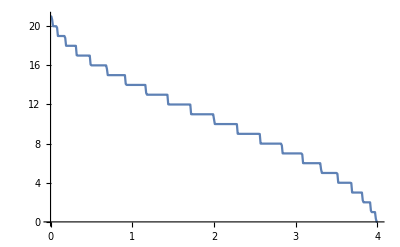
{2810.14,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[0,4,0.01]}]]]
```

```mathematica
φ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,9}], μ2=RandomInteger[{1,9}], μ3=RandomInteger[{1,9}], μ4=RandomInteger[{1,9}],μ5=RandomInteger[{1,9}], μ6=RandomInteger[{10,21}], μ7=RandomInteger[{10,21}], μ8=RandomInteger[{10,21}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2},{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4},{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5},{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[21]-imp1.T[t].SL[ω,0.001,1,0].T[t]].imp1;
Sl12:=Inverse[IdentityMatrix[21]-imp2.T[t].Sl11.T[t]].imp2;
Sl13:=Inverse[IdentityMatrix[21]-imp3.T[t].Sl12.T[t]].imp3;
Sl14:=Inverse[IdentityMatrix[21]-imp4.T[t].Sl13.T[t]].imp4;
Sl15:=Inverse[IdentityMatrix[21]-imp5.T[t].Sl14.T[t]].imp5;
Il1:=Inverse[IdentityMatrix[21]-Sl15.T[t].SR[ω,0.001,1,0].T[t]].Sl15;
Ir1:=Inverse[IdentityMatrix[21]-SR[ω,0.001,1,0].T[t].Sl15.T[t]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
φ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,9}], μ2=RandomInteger[{1,21}], μ3=RandomInteger[{1,9}], μ4=RandomInteger[{1,21}],μ5=RandomInteger[{1,9}], μ6=RandomInteger[{10,21}], μ7=RandomInteger[{10,21}], μ8=RandomInteger[{10,21}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1},{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3},{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5},{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[21]-imp1.T[t].SL[ω,0.001,1,0].T[t]].imp1;
Sl12:=Inverse[IdentityMatrix[21]-imp2.T[t].Sl11.T[t]].imp2;
Sl13:=Inverse[IdentityMatrix[21]-imp3.T[t].Sl12.T[t]].imp3;
Sl14:=Inverse[IdentityMatrix[21]-imp4.T[t].Sl13.T[t]].imp4;
Sl15:=Inverse[IdentityMatrix[21]-imp5.T[t].Sl14.T[t]].imp5;
Il1:=Inverse[IdentityMatrix[21]-Sl15.T[t].SR[ω,0.001,1,0].T[t]].Sl15;
Ir1:=Inverse[IdentityMatrix[21]-SR[ω,0.001,1,0].T[t].Sl15.T[t]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
φ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,9}], μ2=RandomInteger[{1,9}], μ3=RandomInteger[{1,21}], μ4=RandomInteger[{1,21}],μ5=RandomInteger[{1,9}], μ6=RandomInteger[{10,21}], μ7=RandomInteger[{10,21}], μ8=RandomInteger[{10,21}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1},{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2},{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5},{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[21]-imp1.T[t].SL[ω,0.001,1,0].T[t]].imp1;
Sl12:=Inverse[IdentityMatrix[21]-imp2.T[t].Sl11.T[t]].imp2;
Sl13:=Inverse[IdentityMatrix[21]-imp3.T[t].Sl12.T[t]].imp3;
Sl14:=Inverse[IdentityMatrix[21]-imp4.T[t].Sl13.T[t]].imp4;
Sl15:=Inverse[IdentityMatrix[21]-imp5.T[t].Sl14.T[t]].imp5;
Il1:=Inverse[IdentityMatrix[21]-Sl15.T[t].SR[ω,0.001,1,0].T[t]].Sl15;
Ir1:=Inverse[IdentityMatrix[21]-SR[ω,0.001,1,0].T[t].Sl15.T[t]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
φ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,21}], μ2=RandomInteger[{1,9}], μ3=RandomInteger[{1,9}], μ4=RandomInteger[{1,21}],μ5=RandomInteger[{1,9}], μ6=RandomInteger[{10,21}], μ7=RandomInteger[{10,21}], μ8=RandomInteger[{10,21}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2},{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3},{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5},{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[21]-imp1.T[t].SL[ω,0.001,1,0].T[t]].imp1;
Sl12:=Inverse[IdentityMatrix[21]-imp2.T[t].Sl11.T[t]].imp2;
Sl13:=Inverse[IdentityMatrix[21]-imp3.T[t].Sl12.T[t]].imp3;
Sl14:=Inverse[IdentityMatrix[21]-imp4.T[t].Sl13.T[t]].imp4;
Sl15:=Inverse[IdentityMatrix[21]-imp5.T[t].Sl14.T[t]].imp5;
Il1:=Inverse[IdentityMatrix[21]-Sl15.T[t].SR[ω,0.001,1,0].T[t]].Sl15;
Ir1:=Inverse[IdentityMatrix[21]-SR[ω,0.001,1,0].T[t].Sl15.T[t]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
φ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,21}], μ2=RandomInteger[{1,9}], μ3=RandomInteger[{1,9}], μ4=RandomInteger[{1,9}],μ5=RandomInteger[{1,21}], μ6=RandomInteger[{10,21}], μ7=RandomInteger[{10,21}], μ8=RandomInteger[{10,21}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2},{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3},{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4},{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[21]-imp1.T[t].SL[ω,0.001,1,0].T[t]].imp1;
Sl12:=Inverse[IdentityMatrix[21]-imp2.T[t].Sl11.T[t]].imp2;
Sl13:=Inverse[IdentityMatrix[21]-imp3.T[t].Sl12.T[t]].imp3;
Sl14:=Inverse[IdentityMatrix[21]-imp4.T[t].Sl13.T[t]].imp4;
Sl15:=Inverse[IdentityMatrix[21]-imp5.T[t].Sl14.T[t]].imp5;
Il1:=Inverse[IdentityMatrix[21]-Sl15.T[t].SR[ω,0.001,1,0].T[t]].Sl15;
Ir1:=Inverse[IdentityMatrix[21]-SR[ω,0.001,1,0].T[t].Sl15.T[t]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
```

```mathematica
Clear[k21]
```

```mathematica
k81[ω_,ϵ1_]:=k81[ω,ϵ1]=Mean[Mean[Append[{},Table[(φ1[ω,0.001,1,0,ϵ1]+φ2[ω,0.001,1,0,ϵ1]+φ3[ω,0.001,1,0,ϵ1]+φ4[ω,0.001,1,0,ϵ1]+φ5[ω,0.001,1,0,ϵ1])/5,{800}]]]]
```

```mathematica
Timing[k81[1,0.5]]
```

{619.939,13.3411}

```mathematica
Export["/home/shardulmukim/PhD/fwi/21sq/8imp4.csv",Table[{ω,k21[ω,0.4]},{ω,Range[0,4,0.01]}]]
```

$Aborted

```mathematica
Export["/home/shardulmukim/PhD/fwi/21sq/8imp3.csv",Table[{ω,k21[ω,0.3]},{ω,Range[0,4,0.01]}]]
```

```mathematica
Import["/home/shardulmukim/PhD/fwi/21sq/8imp3.csv"]
```

{{0.,16.9205},{0.01,16.2793},{0.02,8.20655},{0.03,10.8626},{0.04,16.1001},{0.05,17.2503},{0.06,17.4123},{0.07,17.0173},{0.08,12.4017},{0.09,9.78109},{0.1,15.9012},{0.11,17.0969},{0.12,17.5474},{0.13,17.6543},{0.14,17.7212},{0.15,17.6738},{0.16,17.5572},{0.17,17.128},{0.18,12.8512},{0.19,11.9863},{0.2,16.1311},{0.21,16.8061},{0.22,17.0457},{0.23,17.157},{0.24,17.214},{0.25,17.2333},{0.26,17.2505},{0.27,17.2235},{0.28,17.1691},{0.29,17.0684},{0.3,16.8815},{0.31,16.3032},{0.32,7.44484},{0.33,13.944},{0.34,15.7855},{0.35,16.1803},{0.36,16.3394},{0.37,16.4167},{0.38,16.4661},{0.39,16.4843},{0.4,16.5033},{0.41,16.5024},{0.42,16.4935},{0.43,16.482},{0.44,16.4579},{0.45,16.4031},{0.46,16.3274},{0.47,16.1775},{0.48,15.7355},{0.49,4.15891},{0.5,13.2242},{0.51,15.0386},{0.52,15.3881},{0.53,15.5132},{0.54,15.5715},{0.55,15.6012},{0.56,15.6209},{0.57,15.6304},{0.58,15.6455},{0.59,15.6457},{0.6,15.6391},{0.61,15.6288},{0.62,15.6199},{0.63,15.5985},{0.64,15.575},{0.65,15.5425},{0.66,15.4666},{0.67,15.3482},{0.68,15.0579},{0.69,12.1776},{0.7,11.5208},{0.71,14.1136},{0.72,14.4751},{0.73,14.5966},{0.74,14.6579},{0.75,14.6886},{0.76,14.7111},{0.77,14.7242},{0.78,14.7296},{0.79,14.7309},{0.8,14.7318},{0.81,14.7291},{0.82,14.7271},{0.83,14.7183},{0.84,14.7106},{0.85,14.6981},{0.86,14.6834},{0.87,14.6523},{0.88,14.6157},{0.89,14.5454},{0.9,14.4356},{0.91,14.1223},{0.92,6.19433},{0.93,11.9414},{0.94,13.3868},{0.95,13.6111},{0.96,13.6934},{0.97,13.7347},{0.98,13.7578},{0.99,13.7733},{1.,13.7842},{1.01,13.7871},{1.02,13.7908},{1.03,13.7928},{1.04,13.7906},{1.05,13.7924},{1.06,13.7862},{1.07,13.7804},{1.08,13.775},{1.09,13.7695},{1.1,13.7546},{1.11,13.7395},{1.12,13.7144},{1.13,13.6772},{1.14,13.6259},{1.15,13.5195},{1.16,13.2613},{1.17,8.39136},{1.18,11.1882},{1.19,12.469},{1.2,12.6788},{1.21,12.7497},{1.22,12.7834},{1.23,12.803},{1.24,12.817},{1.25,12.8237},{1.26,12.8309},{1.27,12.8312},{1.28,12.8335},{1.29,12.8359},{1.3,12.8319},{1.31,12.8326},{1.32,12.8278},{1.33,12.8228},{1.34,12.8173},{1.35,12.811},{1.36,12.8028},{1.37,12.7906},{1.38,12.7731},{1.39,12.7484},{1.4,12.7142},{1.41,12.6528},{1.42,12.5439},{1.43,12.1959},{1.44,4.55573},{1.45,11.0303},{1.46,11.6218},{1.47,11.7499},{1.48,11.8023},{1.49,11.8256},{1.5,11.8423},{1.51,11.8544},{1.52,11.8578},{1.53,11.861},{1.54,11.8633},{1.55,11.8653},{1.56,11.8645},{1.57,11.8634},{1.58,11.8613},{1.59,11.8595},{1.6,11.8578},{1.61,11.8514},{1.62,11.8473},{1.63,11.8421},{1.64,11.8327},{1.65,11.8221},{1.66,11.8048},{1.67,11.7841},{1.68,11.7518},{1.69,11.6927},{1.7,11.5857},{1.71,11.2158},{1.72,5.38707},{1.73,10.3318},{1.74,10.7166},{1.75,10.8033},{1.76,10.8412},{1.77,10.8593},{1.78,10.8702},{1.79,10.8789},{1.8,10.8828},{1.81,10.8855},{1.82,10.8866},{1.83,10.8874},{1.84,10.8863},{1.85,10.8857},{1.86,10.8839},{1.87,10.8825},{1.88,10.8784},{1.89,10.8758},{1.9,10.8709},{1.91,10.8655},{1.92,10.8574},{1.93,10.8472},{1.94,10.835},{1.95,10.8207},{1.96,10.7915},{1.97,10.7538},{1.98,10.6782},{1.99,10.5065},{2.,8.85125},{2.01,8.31163},{2.02,9.64646},{2.03,9.79993},{2.04,9.84927},{2.05,9.87172},{2.06,9.88868},{2.07,9.89525},{2.08,9.89971},{2.09,9.90374},{2.1,9.90384},{2.11,9.90417},{2.12,9.90557},{2.13,9.9052},{2.14,9.90302},{2.15,9.9018},{2.16,9.89956},{2.17,9.89566},{2.18,9.89285},{2.19,9.8887},{2.2,9.88317},{2.21,9.87414},{2.22,9.863},{2.23,9.84999},{2.24,9.82993},{2.25,9.8013},{2.26,9.75446},{2.27,9.657},{2.28,9.30623},{2.29,5.33416},{2.3,8.56994},{2.31,8.80478},{2.32,8.86543},{2.33,8.88929},{2.34,8.90182},{2.35,8.90906},{2.36,8.91326},{2.37,8.91649},{2.38,8.91783},{2.39,8.91782},{2.4,8.91754},{2.41,8.91797},{2.42,8.91697},{2.43,8.91494},{2.44,8.91272},{2.45,8.90927},{2.46,8.90568},{2.47,8.90041},{2.48,8.89506},{2.49,8.88679},{2.5,8.87751},{2.51,8.86412},{2.52,8.84473},{2.53,8.81527},{2.54,8.76536},{2.55,8.66047},{2.56,8.25019},{2.57,5.44148},{2.58,7.6903},{2.59,7.84244},{2.6,7.88507},{2.61,7.90633},{2.62,7.91603},{2.63,7.92266},{2.64,7.92432},{2.65,7.92758},{2.66,7.92787},{2.67,7.9275},{2.68,7.92788},{2.69,7.9268},{2.7,7.92517},{2.71,7.92209},{2.72,7.91984},{2.73,7.91655},{2.74,7.91173},{2.75,7.90548},{2.76,7.89829},{2.77,7.88799},{2.78,7.87456},{2.79,7.85397},{2.8,7.82446},{2.81,7.76976},{2.82,7.641},{2.83,6.83504},{2.84,6.01769},{2.85,6.78981},{2.86,6.87832},{2.87,6.90731},{2.88,6.92229},{2.89,6.92842},{2.9,6.93279},{2.91,6.93499},{2.92,6.93602},{2.93,6.93574},{2.94,6.9358},{2.95,6.93437},{2.96,6.93209},{2.97,6.92943},{2.98,6.9271},{2.99,6.92161},{3.,6.91754},{3.01,6.90915},{3.02,6.90042},{3.03,6.88857},{3.04,6.87078},{3.05,6.84325},{3.06,6.79074},{3.07,6.67636},{3.08,6.05796},{3.09,4.96815},{3.1,5.81823},{3.11,5.89247},{3.12,5.91996},{3.13,5.93106},{3.14,5.93715},{3.15,5.94071},{3.16,5.94086},{3.17,5.9422},{3.18,5.94033},{3.19,5.93864},{3.2,5.9366},{3.21,5.9339},{3.22,5.93006},{3.23,5.92429},{3.24,5.91616},{3.25,5.90685},{3.26,5.89435},{3.27,5.87558},{3.28,5.84339},{3.29,5.78976},{3.3,5.66315},{3.31,4.54389},{3.32,4.40602},{3.33,4.86008},{3.34,4.91649},{3.35,4.93262},{3.36,4.94175},{3.37,4.9448},{3.38,4.94648},{3.39,4.94744},{3.4,4.94579},{3.41,4.94357},{3.42,4.9393},{3.43,4.93524},{3.44,4.93009},{3.45,4.92104},{3.46,4.9103},{3.47,4.89402},{3.48,4.86901},{3.49,4.82349},{3.5,4.72453},{3.51,4.22969},{3.52,3.35148},{3.53,3.87165},{3.54,3.92345},{3.55,3.94071},{3.56,3.94558},{3.57,3.94798},{3.58,3.94743},{3.59,3.94495},{3.6,3.94022},{3.61,3.93523},{3.62,3.92572},{3.63,3.91569},{3.64,3.89881},{3.65,3.87401},{3.66,3.83121},{3.67,3.73778},{3.68,3.37175},{3.69,2.22129},{3.7,2.87188},{3.71,2.92747},{3.72,2.93952},{3.73,2.94338},{3.74,2.94162},{3.75,2.9381},{3.76,2.92957},{3.77,2.91966},{3.78,2.90335},{3.79,2.87752},{3.8,2.82636},{3.81,2.71274},{3.82,1.75172},{3.83,1.75259},{3.84,1.90735},{3.85,1.92621},{3.86,1.92316},{3.87,1.91378},{3.88,1.89763},{3.89,1.86964},{3.9,1.81142},{3.91,1.68351},{3.92,0.764046},{3.93,0.775125},{3.94,0.894613},{3.95,0.889583},{3.96,0.856437},{3.97,0.753893},{3.98,0.122687},{3.99,0.13322},{4.,0.0220198}}

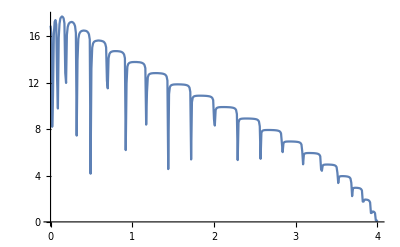

```mathematica
ListPlot[%66,Joined->True]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/21sq/8imp6.csv",Table[{ω,k21[ω,0.6]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/21sq/8imp6.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/21sq/8imp7.csv",Table[{ω,k21[ω,0.7]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/21sq/8imp7.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/21sq/8imp8.csv",Table[{ω,k21[ω,0.8]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/21sq/8imp8.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/21sq/8imp9.csv",Table[{ω,k21[ω,0.9]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/21sq/8imp9.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/21sq/8imp1.csv",Table[{ω,k21[ω,1]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/21sq/8imp1.csv

```mathematica
Import["/home/shardulmukim/PhD/fwi/21sq/8imp1.csv"]
```

{{0.,8.44313},{0.01,7.90242},{0.02,6.68449},{0.03,11.5757},{0.04,6.0678},{0.05,4.79363},{0.06,6.02093},{0.07,6.75634},{0.08,5.29222},{0.09,5.09003},{0.1,3.94788},{0.11,3.87522},{0.12,5.57464},{0.13,7.28483},{0.14,8.46697},{0.15,9.48224},{0.16,9.74931},{0.17,9.52956},{0.18,7.12131},{0.19,4.3291},{0.2,3.15592},{0.21,4.54777},{0.22,6.68544},{0.23,8.48934},{0.24,9.75811},{0.25,10.5075},{0.26,11.0361},{0.27,11.2296},{0.28,11.4798},{0.29,11.5219},{0.3,11.3403},{0.31,10.8039},{0.32,7.08051},{0.33,4.20537},{0.34,3.82353},{0.35,5.44879},{0.36,7.56789},{0.37,9.15108},{0.38,10.0931},{0.39,10.7982},{0.4,11.2967},{0.41,11.7615},{0.42,11.8723},{0.43,12.0674},{0.44,12.1074},{0.45,12.1095},{0.46,12.0332},{0.47,11.8384},{0.48,11.3277},{0.49,8.41447},{0.5,4.82676},{0.51,4.05042},{0.52,5.64026},{0.53,7.65824},{0.54,9.13851},{0.55,10.1841},{0.56,10.864},{0.57,11.2748},{0.58,11.6062},{0.59,11.8564},{0.6,12.0213},{0.61,12.1562},{0.62,12.1862},{0.63,12.2262},{0.64,12.1879},{0.65,12.1707},{0.66,12.0427},{0.67,11.8153},{0.68,11.4135},{0.69,10.0001},{0.7,5.94353},{0.71,4.50493},{0.72,5.2336},{0.73,6.99817},{0.74,8.35982},{0.75,9.5827},{0.76,10.2637},{0.77,10.8961},{0.78,11.1913},{0.79,11.4586},{0.8,11.6197},{0.81,11.7428},{0.82,11.821},{0.83,11.8956},{0.84,11.924},{0.85,11.9159},{0.86,11.9413},{0.87,11.8525},{0.88,11.7974},{0.89,11.6656},{0.9,11.4468},{0.91,11.0028},{0.92,9.11784},{0.93,5.81024},{0.94,4.59553},{0.95,5.37788},{0.96,6.89145},{0.97,8.25965},{0.98,9.31163},{0.99,10.0398},{1.,10.4339},{1.01,10.7742},{1.02,11.0762},{1.03,11.1532},{1.04,11.2733},{1.05,11.3612},{1.06,11.4291},{1.07,11.4217},{1.08,11.4583},{1.09,11.4758},{1.1,11.4418},{1.11,11.4377},{1.12,11.3816},{1.13,11.2801},{1.14,11.1721},{1.15,10.9478},{1.16,10.624},{1.17,9.14228},{1.18,5.80963},{1.19,4.37596},{1.2,4.60617},{1.21,6.35952},{1.22,7.69555},{1.23,8.7856},{1.24,9.36974},{1.25,9.89765},{1.26,10.1851},{1.27,10.3745},{1.28,10.554},{1.29,10.6641},{1.3,10.7542},{1.31,10.8025},{1.32,10.8544},{1.33,10.8593},{1.34,10.866},{1.35,10.8736},{1.36,10.8599},{1.37,10.8536},{1.38,10.816},{1.39,10.7264},{1.4,10.6294},{1.41,10.5276},{1.42,10.3164},{1.43,9.89261},{1.44,8.18241},{1.45,5.45681},{1.46,4.35015},{1.47,4.77062},{1.48,5.93293},{1.49,7.36025},{1.5,8.26774},{1.51,8.86413},{1.52,9.28121},{1.53,9.60235},{1.54,9.76514},{1.55,9.88624},{1.56,10.0024},{1.57,10.0863},{1.58,10.1201},{1.59,10.1542},{1.6,10.1907},{1.61,10.1943},{1.62,10.2144},{1.63,10.1773},{1.64,10.1725},{1.65,10.1585},{1.66,10.0998},{1.67,10.0416},{1.68,9.95746},{1.69,9.80644},{1.7,9.59944},{1.71,9.17313},{1.72,7.20775},{1.73,4.99002},{1.74,3.91793},{1.75,4.45735},{1.76,5.81321},{1.77,6.93053},{1.78,7.73658},{1.79,8.27165},{1.8,8.65438},{1.81,8.90239},{1.82,9.07378},{1.83,9.21333},{1.84,9.26802},{1.85,9.33914},{1.86,9.39581},{1.87,9.41206},{1.88,9.43417},{1.89,9.45205},{1.9,9.44038},{1.91,9.43493},{1.92,9.42253},{1.93,9.38115},{1.94,9.34964},{1.95,9.29073},{1.96,9.24097},{1.97,9.12642},{1.98,8.95752},{1.99,8.69419},{2.,7.85729},{2.01,6.06952},{2.02,4.61933},{2.03,4.36118},{2.04,4.55563},{2.05,5.33981},{2.06,6.39212},{2.07,6.96914},{2.08,7.52086},{2.09,7.83695},{2.1,8.15087},{2.11,8.31947},{2.12,8.38494},{2.13,8.4702},{2.14,8.53851},{2.15,8.57254},{2.16,8.61457},{2.17,8.60747},{2.18,8.62701},{2.19,8.63475},{2.2,8.61656},{2.21,8.58263},{2.22,8.54917},{2.23,8.51559},{2.24,8.47035},{2.25,8.37211},{2.26,8.24419},{2.27,8.06245},{2.28,7.681},{2.29,6.32069},{2.3,4.35109},{2.31,3.35466},{2.32,3.32838},{2.33,4.3349},{2.34,5.4065},{2.35,6.16328},{2.36,6.7978},{2.37,7.13987},{2.38,7.36101},{2.39,7.50635},{2.4,7.61206},{2.41,7.66189},{2.42,7.71874},{2.43,7.74619},{2.44,7.76048},{2.45,7.80483},{2.46,7.78388},{2.47,7.79537},{2.48,7.7716},{2.49,7.7497},{2.5,7.71879},{2.51,7.68246},{2.52,7.61709},{2.53,7.53725},{2.54,7.41819},{2.55,7.22683},{2.56,6.84674},{2.57,5.65018},{2.58,4.06079},{2.59,3.01371},{2.6,2.87093},{2.61,3.71299},{2.62,4.48691},{2.63,5.3543},{2.64,5.96362},{2.65,6.28866},{2.66,6.51069},{2.67,6.6591},{2.68,6.75186},{2.69,6.81292},{2.7,6.87245},{2.71,6.88928},{2.72,6.91196},{2.73,6.9035},{2.74,6.91175},{2.75,6.89424},{2.76,6.87386},{2.77,6.85263},{2.78,6.79358},{2.79,6.74956},{2.8,6.65694},{2.81,6.52086},{2.82,6.31773},{2.83,5.8418},{2.84,4.63237},{2.85,3.30344},{2.86,2.62634},{2.87,2.6221},{2.88,3.27962},{2.89,4.08799},{2.9,4.84385},{2.91,5.22792},{2.92,5.58151},{2.93,5.7286},{2.94,5.83501},{2.95,5.92482},{2.96,5.95797},{2.97,5.98607},{2.98,5.9913},{2.99,6.00404},{3.,5.99968},{3.01,5.97311},{3.02,5.96191},{3.03,5.91279},{3.04,5.86491},{3.05,5.78403},{3.06,5.65454},{3.07,5.4712},{3.08,5.07219},{3.09,4.10135},{3.1,2.98924},{3.11,2.24459},{3.12,2.1551},{3.13,2.53133},{3.14,3.31174},{3.15,3.9021},{3.16,4.37882},{3.17,4.68893},{3.18,4.8554},{3.19,4.95055},{3.2,5.0079},{3.21,5.04053},{3.22,5.05376},{3.23,5.07106},{3.24,5.05328},{3.25,5.02365},{3.26,5.00236},{3.27,4.94552},{3.28,4.86979},{3.29,4.74329},{3.3,4.54369},{3.31,4.10701},{3.32,3.30566},{3.33,2.57874},{3.34,1.97502},{3.35,1.89127},{3.36,2.04059},{3.37,2.64048},{3.38,3.11247},{3.39,3.51694},{3.4,3.7876},{3.41,3.91772},{3.42,4.03083},{3.43,4.08101},{3.44,4.10723},{3.45,4.09917},{3.46,4.07775},{3.47,4.04911},{3.48,3.97255},{3.49,3.89354},{3.5,3.71286},{3.51,3.36035},{3.52,2.73531},{3.53,2.24156},{3.54,1.90151},{3.55,1.85598},{3.56,1.85305},{3.57,2.10624},{3.58,2.40888},{3.59,2.7524},{3.6,2.91805},{3.61,3.03159},{3.62,3.09504},{3.63,3.10283},{3.64,3.08385},{3.65,3.0428},{3.66,2.951},{3.67,2.8188},{3.68,2.54662},{3.69,2.15894},{3.7,1.86925},{3.71,1.89604},{3.72,2.05138},{3.73,1.92881},{3.74,1.86296},{3.75,1.80404},{3.76,1.76638},{3.77,1.80626},{3.78,1.92604},{3.79,1.96207},{3.8,1.90801},{3.81,1.75164},{3.82,1.43821},{3.83,1.311},{3.84,1.44902},{3.85,2.437},{3.86,2.67766},{3.87,2.37473},{3.88,1.96495},{3.89,1.37723},{3.9,1.00056},{3.91,0.730012},{3.92,0.504918},{3.93,0.61013},{3.94,1.12325},{3.95,2.76739},{3.96,6.65989},{3.97,8.64385},{3.98,14.3841},{3.99,9.12022},{4.,4.80354}}

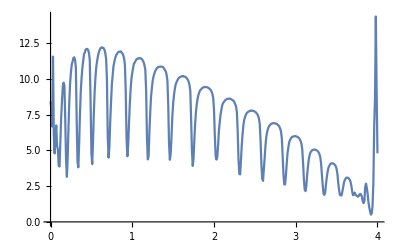

```mathematica
ListPlot[%287,Joined->True]
```

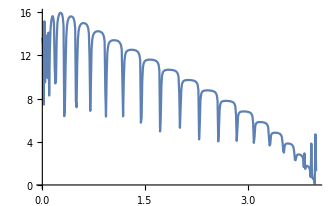

```mathematica
ListPlot[%155,Joined->True]
```

```mathematica
Timing[k21[0,0.5]]
```

{123.11,13.4895}

```mathematica
Timing[k21[0,0.5]]
```

{132.349,13.4694}

```mathematica
k21[1.01,0.5]
```

13.4198

```mathematica
μ1=RandomInteger[{1,21}] ; μ2=RandomInteger[{1,9}] ; μ3=RandomInteger[{1,21}] ; μ4=RandomInteger[{1,9}] ; μ5=RandomInteger[{1,9}] ; μ6=RandomInteger[{10,21}] ; μ7=RandomInteger[{10,21}];   μ8=RandomInteger[{10,21}];Print[{μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8}]
```

{19,2,18,7,5,12,18,17}

```mathematica
test1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2},{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4},{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5},{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[21]-imp1.T[t].SL[ω,δ,t,ϵ].T[t]].imp1;
Sl12:=Inverse[IdentityMatrix[21]-imp2.T[t].Sl11.T[t]].imp2;
Sl13:=Inverse[IdentityMatrix[21]-imp3.T[t].Sl12.T[t]].imp3;
Sl14:=Inverse[IdentityMatrix[21]-imp4.T[t].Sl13.T[t]].imp4;
Sl15:=Inverse[IdentityMatrix[21]-imp5.T[t].Sl14.T[t]].imp5;
Il1:=Inverse[IdentityMatrix[21]-Sl15.T[t].SR[ω,δ,t,ϵ].T[t]].Sl15;
Ir1:=Inverse[IdentityMatrix[21]-SR[ω,δ,t,ϵ].T[t].Sl15.T[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
```

```mathematica
Clear[m1]
```

```mathematica
m1[ϵ1_]:=m1[ϵ1]=Table[{ω,test1[ω,0.001,1,0,ϵ1]},{ω,Range[0,4,0.01]}]
```

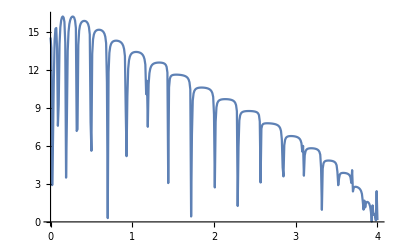

```mathematica
ListLinePlot[m1[0.5]]
```

```mathematica
ρ33:=Module[{B1=Transpose[{m1[00][[1;;400]][[;;,1]],(m1[0.5][[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/21sq/8imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ34:=Module[{B1=Transpose[{m1[0.0][[1;;400]][[;;,1]],(m1[0.5][[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/21sq/8imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ35:=Module[{B1=Transpose[{m1[0.0][[1;;400]][[;;,1]],(m1[0.5][[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/21sq/8imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ36:=Module[{B1=Transpose[{m1[0.0][[1;;400]][[;;,1]],(m1[0.5][[1;;400,2]]-Import["/home/shardulmukim/PhD/fwi/21sq/8imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ37:=Module[{B1=Transpose[{m1[0.0][[1;;400]][[;;,1]],(m1[0.5][[1;;400,2]]-Import["/home/shardulmukim/PhD/fwi/21sq/8imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ38:=Module[{B1=Transpose[{m1[0.0][[1;;400]][[;;,1]],(m1[0.5][[1;;400,2]]-Import["/home/shardulmukim/PhD/fwi/21sq/8imp8.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ39:=Module[{B1=Transpose[{m1[0.0][[1;;400]][[;;,1]],(m1[0.5][[1;;400,2]]-Import["/home/shardulmukim/PhD/fwi/21sq/8imp9.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
A3:= {{3,ρ33},{4,ρ34},{5,ρ35},{6,ρ36},{7,ρ33},{8,ρ38},{9,ρ39}}
```

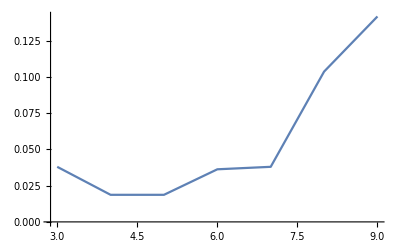

```mathematica
ListLinePlot[A3]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,21}]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{gg=g[ω,δ,t,ϵ],T=t*IdentityMatrix[21],imp=imp[ω,δ,t,ϵ,ϵ1],m=RandomInteger[{0,2}],n=RandomInteger[{0,2}],o=RandomInteger[{0,2}],p=RandomInteger[{0,2}],q=RandomInteger[{0,2}]},sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[21]-gg.T.J.T].gg,n]; J=J];sl2=Inverse[IdentityMatrix[21]-imp.T.sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[21]-gg.T.J.T].gg,m]; J=J];sl4=Inverse[IdentityMatrix[21]-imp.T.sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[21]-gg.T.J.T].gg,o]; J=J];sl6=Inverse[IdentityMatrix[21]-imp.T.sl5.T].imp; sl7=Module[{J=sl6},Do[J=Inverse[IdentityMatrix[21]-gg.T.J.T].gg,p]; J=J];sl8=Inverse[IdentityMatrix[21]-imp.T.sl7.T].imp; sl9=Module[{J=sl8},Do[J=Inverse[IdentityMatrix[21]-gg.T.J.T].gg,q]; J=J];Il1:=Inverse[IdentityMatrix[21]-sl9.T1[1].SR[ω,0.001,1,0].T1[1]].sl9;
Ir1:=Inverse[IdentityMatrix[21]-SR[ω,δ,1,0].T1[1].sl9.T1[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
Export["21sq4imp3.csv",Table[{ω,Mean[Table[tr1[ω,0.01,1,0,0.3],1500]]},{ω,Range[0,4,0.01]}]]
```

21sq4imp3.csv

```mathematica
Export["21sq4imp4.csv",Table[{ω,Mean[Table[tr1[ω,0.01,1,0,0.4],1500]]},{ω,Range[0,4,0.01]}]]
```

21sq4imp4.csv

```mathematica
Export["21sq4imp5.csv",Table[{ω,Mean[Table[tr1[ω,0.01,1,0,0.5],1500]]},{ω,Range[0,4,0.01]}]]
```

21sq4imp5.csv

```mathematica
Export["21sq4imp6.csv",Table[{ω,Mean[Table[tr1[ω,0.01,1,0,0.6],1500]]},{ω,Range[0,4,0.01]}]]
```

21sq4imp6.csv

```mathematica
Export["21sq4imp7.csv",Table[{ω,Mean[Table[tr1[ω,0.01,1,0,0.7],1500]]},{ω,Range[0,4,0.01]}]]
```

21sq4imp7.csv

```mathematica
Export["21sq4imp8.csv",Table[{ω,Mean[Table[tr1[ω,0.01,1,0,0.8],1500]]},{ω,Range[0,4,0.01]}]]
```

21sq4imp8.csv

```mathematica
Export["21sq4imp9.csv",Table[{ω,Mean[Table[tr1[ω,0.01,1,0,0.9],1500]]},{ω,Range[0,4,0.01]}]]
```

21sq4imp9.csv

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.01,1,0,1],1500]]},{ω,Range[0,4,0.01]}]
```

{{0.,14.2311},{0.01,13.7712},{0.02,8.80856},{0.03,13.3047},{0.04,14.6738},{0.05,15.0045},{0.06,15.097},{0.07,14.4491},{0.08,10.8385},{0.09,12.8758},{0.1,14.5158},{0.11,15.2517},{0.12,15.6171},{0.13,15.8506},{0.14,15.8332},{0.15,15.8529},{0.16,15.4617},{0.17,14.7099},{0.18,11.0606},{0.19,13.0929},{0.2,14.2766},{0.21,15.1145},{0.22,15.5507},{0.23,15.7303},{0.24,15.845},{0.25,15.8477},{0.26,15.865},{0.27,15.7975},{0.28,15.6644},{0.29,15.4296},{0.3,14.9415},{0.31,13.9731},{0.32,11.3739},{0.33,12.8837},{0.34,14.0517},{0.35,14.8094},{0.36,15.1037},{0.37,15.3342},{0.38,15.445},{0.39,15.4441},{0.4,15.4688},{0.41,15.4408},{0.42,15.4161},{0.43,15.3252},{0.44,15.2414},{0.45,15.1004},{0.46,14.8392},{0.47,14.4051},{0.48,13.5311},{0.49,10.1844},{0.5,12.3999},{0.51,13.2688},{0.52,14.069},{0.53,14.435},{0.54,14.6644},{0.55,14.7193},{0.56,14.7883},{0.57,14.7992},{0.58,14.8217},{0.59,14.8106},{0.6,14.7945},{0.61,14.7447},{0.62,14.6785},{0.63,14.605},{0.64,14.5148},{0.65,14.3636},{0.66,14.0871},{0.67,13.7999},{0.68,13.0805},{0.69,9.80091},{0.7,11.4379},{0.71,12.3609},{0.72,13.2938},{0.73,13.6753},{0.74,13.8455},{0.75,13.939},{0.76,14.017},{0.77,14.026},{0.78,14.0507},{0.79,14.0461},{0.8,14.0499},{0.81,14.0421},{0.82,14.0076},{0.83,13.9784},{0.84,13.9326},{0.85,13.8618},{0.86,13.7845},{0.87,13.6882},{0.88,13.5332},{0.89,13.2739},{0.9,12.922},{0.91,12.165},{0.92,9.10479},{0.93,11.4827},{0.94,11.5833},{0.95,12.5089},{0.96,12.8933},{0.97,13.0336},{0.98,13.1032},{0.99,13.18},{1.,13.2139},{1.01,13.2135},{1.02,13.2228},{1.03,13.2201},{1.04,13.214},{1.05,13.1986},{1.06,13.1815},{1.07,13.154},{1.08,13.1332},{1.09,13.0779},{1.1,13.0364},{1.11,12.9333},{1.12,12.87},{1.13,12.6871},{1.14,12.4693},{1.15,12.1283},{1.16,11.4485},{1.17,8.53403},{1.18,9.88902},{1.19,10.9141},{1.2,11.8038},{1.21,12.0949},{1.22,12.2094},{1.23,12.2612},{1.24,12.3038},{1.25,12.346},{1.26,12.3476},{1.27,12.3364},{1.28,12.3479},{1.29,12.3397},{1.3,12.3354},{1.31,12.3406},{1.32,12.3068},{1.33,12.2956},{1.34,12.2686},{1.35,12.2297},{1.36,12.1903},{1.37,12.1404},{1.38,12.0503},{1.39,11.9692},{1.4,11.7921},{1.41,11.5461},{1.42,11.1902},{1.43,10.3234},{1.44,8.99649},{1.45,9.46702},{1.46,10.4003},{1.47,11.0572},{1.48,11.2781},{1.49,11.3674},{1.5,11.4111},{1.51,11.4343},{1.52,11.4526},{1.53,11.4637},{1.54,11.4625},{1.55,11.4568},{1.56,11.4607},{1.57,11.4529},{1.58,11.4451},{1.59,11.4212},{1.6,11.4211},{1.61,11.402},{1.62,11.3764},{1.63,11.3488},{1.64,11.3154},{1.65,11.2454},{1.66,11.1765},{1.67,11.0739},{1.68,10.9215},{1.69,10.7062},{1.7,10.3558},{1.71,9.41262},{1.72,8.47822},{1.73,8.64924},{1.74,9.81729},{1.75,10.344},{1.76,10.4576},{1.77,10.4902},{1.78,10.5169},{1.79,10.5313},{1.8,10.5367},{1.81,10.5436},{1.82,10.554},{1.83,10.5506},{1.84,10.5477},{1.85,10.5386},{1.86,10.5453},{1.87,10.5236},{1.88,10.5111},{1.89,10.5006},{1.9,10.4856},{1.91,10.4525},{1.92,10.4252},{1.93,10.3722},{1.94,10.3184},{1.95,10.2222},{1.96,10.0968},{1.97,9.90244},{1.98,9.54456},{1.99,8.81054},{2.,6.30877},{2.01,9.06817},{2.02,7.71762},{2.03,9.01006},{2.04,9.43972},{2.05,9.51717},{2.06,9.54909},{2.07,9.57566},{2.08,9.58431},{2.09,9.59987},{2.1,9.60092},{2.11,9.59885},{2.12,9.59838},{2.13,9.59633},{2.14,9.59198},{2.15,9.58327},{2.16,9.57671},{2.17,9.56865},{2.18,9.55353},{2.19,9.5324},{2.2,9.49799},{2.21,9.47073},{2.22,9.41902},{2.23,9.35261},{2.24,9.26682},{2.25,9.12652},{2.26,8.91538},{2.27,8.52975},{2.28,7.52266},{2.29,7.53116},{2.3,7.21356},{2.31,8.13825},{2.32,8.56616},{2.33,8.60916},{2.34,8.6253},{2.35,8.64384},{2.36,8.65515},{2.37,8.65935},{2.38,8.65954},{2.39,8.66062},{2.4,8.66045},{2.41,8.66341},{2.42,8.66115},{2.43,8.65386},{2.44,8.64309},{2.45,8.63474},{2.46,8.61791},{2.47,8.5992},{2.48,8.57637},{2.49,8.5387},{2.5,8.4971},{2.51,8.42812},{2.52,8.33241},{2.53,8.19114},{2.54,7.97738},{2.55,7.57089},{2.56,6.40026},{2.57,6.6638},{2.58,6.72468},{2.59,7.41719},{2.6,7.66631},{2.61,7.6819},{2.62,7.69394},{2.63,7.70541},{2.64,7.70931},{2.65,7.70925},{2.66,7.71942},{2.67,7.71975},{2.68,7.7142},{2.69,7.71428},{2.7,7.70109},{2.71,7.70097},{2.72,7.68634},{2.73,7.67741},{2.74,7.65955},{2.75,7.62791},{2.76,7.59264},{2.77,7.54735},{2.78,7.47318},{2.79,7.37202},{2.8,7.22564},{2.81,6.97046},{2.82,6.47905},{2.83,4.714},{2.84,6.00246},{2.85,5.93419},{2.86,6.60214},{2.87,6.74446},{2.88,6.7373},{2.89,6.74727},{2.9,6.7565},{2.91,6.76588},{2.92,6.76307},{2.93,6.77098},{2.94,6.76457},{2.95,6.76518},{2.96,6.75921},{2.97,6.7484},{2.98,6.73441},{2.99,6.71615},{3.,6.69088},{3.01,6.65531},{3.02,6.61048},{3.03,6.54571},{3.04,6.44163},{3.05,6.30255},{3.06,6.05117},{3.07,5.58367},{3.08,4.08429},{3.09,5.01714},{3.1,5.18514},{3.11,5.76843},{3.12,5.808},{3.13,5.80648},{3.14,5.80367},{3.15,5.80959},{3.16,5.8111},{3.17,5.81393},{3.18,5.80535},{3.19,5.80528},{3.2,5.79568},{3.21,5.77972},{3.22,5.76049},{3.23,5.73705},{3.24,5.70334},{3.25,5.65227},{3.26,5.58813},{3.27,5.4803},{3.28,5.31411},{3.29,5.06318},{3.3,4.52217},{3.31,4.01014},{3.32,4.0865},{3.33,4.41703},{3.34,4.85365},{3.35,4.84876},{3.36,4.83966},{3.37,4.84159},{3.38,4.82981},{3.39,4.82877},{3.4,4.81963},{3.41,4.80647},{3.42,4.8008},{3.43,4.77253},{3.44,4.7402},{3.45,4.69424},{3.46,4.62698},{3.47,4.53019},{3.48,4.37667},{3.49,4.12884},{3.5,3.64872},{3.51,2.7959},{3.52,3.56908},{3.53,3.67302},{3.54,3.88395},{3.55,3.84856},{3.56,3.82585},{3.57,3.81949},{3.58,3.80744},{3.59,3.79443},{3.6,3.77735},{3.61,3.74323},{3.62,3.68866},{3.63,3.63258},{3.64,3.5354},{3.65,3.39283},{3.66,3.14533},{3.67,2.70825},{3.68,2.06799},{3.69,2.74805},{3.7,2.68411},{3.71,2.75787},{3.72,2.75283},{3.73,2.74232},{3.74,2.71405},{3.75,2.68638},{3.76,2.63135},{3.77,2.55863},{3.78,2.44373},{3.79,2.25779},{3.8,1.9774},{3.81,1.3898},{3.82,2.21369},{3.83,1.71549},{3.84,1.64396},{3.85,1.52753},{3.86,1.49612},{3.87,1.44256},{3.88,1.33658},{3.89,1.14222},{3.9,0.842249},{3.91,0.594847},{3.92,2.36607},{3.93,1.07649},{3.94,0.905057},{3.95,0.647081},{3.96,0.39544},{3.97,0.454964},{3.98,1.54004},{3.99,0.615661},{4.,0.779444}}

```mathematica
Export["21sq4imp1.csv",%56]
```

21sq4imp1.csv

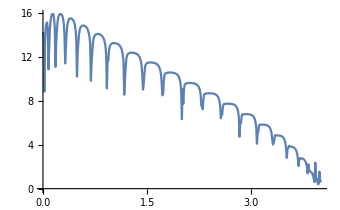

```mathematica
ListPlot[%56,Joined->True],
```